```mathematica
Monitor[
Select[
Flatten[
Table[
With[
{g=ReadGrof[i]},
Table[
With[
{f=FindFace[g,e]},
{i,e,CalcQuadri[g,f], ContainsRule1Reduction[i], Chrom[i]/24}
]
,{e,EdgeList[g]}]
]
,{i,1,2000}],
1],
!#[[3,7]]&&Abs[#[[3,6]]]>1&

],{i,e}]
```

{{111,3<->5,{22,19,2,17,2,2,False,{6,6,7,4}},False,20},{114,2<->3,{37,53,32,21,16,-2,False,{7,3,7,6}},True,5},{204,2<->3,{16,18,4,14,2,2,False,{6,3,8,5}},True,12},{204,2<->7,{22,31,10,21,10,-2,False,{6,8,5,6}},True,12},{209,4<->6,{22,31,10,21,10,-2,False,{5,8,5,6}},True,12},{211,4<->8,{22,31,10,21,10,-2,False,{5,8,5,6}},True,12},{212,7<->8,{22,31,10,21,10,-2,False,{6,8,5,6}},True,12},{213,7<->8,{22,31,10,21,10,-2,False,{6,7,5,7}},True,12},{229,2<->7,{21,33,16,17,12,-3,False,{7,7,6,6}},True,5},{235,2<->6,{21,33,16,17,12,-3,False,{7,7,6,6}},True,5},{285,3<->5,{12,9,8,1,0,2,False,{8,6,7,3}},True,4},{290,3<->5,{33,40,32,8,8,2,False,{9,5,8,3}},True,1},{314,3<->5,{37,53,32,21,16,-2,False,{8,5,7,6}},True,5},{321,3<->5,{36,52,32,20,16,-2,False,{7,5,8,6}},True,4},{352,5<->8,{16,18,4,14,2,2,False,{8,3,6,5}},True,12},{352,6<->8,{22,31,10,21,10,-2,False,{5,7,6,8}},True,12},{383,2<->3,{30,35,10,25,10,-2,False,{5,4,7,8}},False,20},{385,2<->3,{60,84,48,36,24,-2,False,{5,3,7,8}},True,12},{396,2<->3,{45,65,40,25,20,-3,False,{6,3,8,7}},True,5},{443,3<->5,{24,28,8,20,4,3,False,{8,5,8,5}},False,16},{446,5<->6,{32,40,16,24,8,2,False,{8,7,6,3}},True,16},{453,5<->6,{36,52,32,20,16,-2,False,{9,7,6,3}},True,4},{456,2<->3,{20,25,8,17,8,-2,False,{6,4,7,7}},False,12},{456,2<->5,{22,29,10,19,10,-2,False,{6,7,7,4}},False,12},{461,3<->5,{22,19,2,17,2,2,False,{6,6,8,4}},True,20},{466,3<->5,{12,9,8,1,0,2,False,{8,5,8,6}},True,4},{467,3<->5,{12,9,8,1,0,2,False,{8,5,8,5}},True,4},{471,5<->6,{36,52,32,20,16,-2,False,{8,7,6,3}},True,4},{487,2<->9,{22,31,10,21,10,-2,False,{6,8,5,7}},True,12},{488,6<->9,{22,31,10,21,10,-2,False,{6,8,5,7}},True,12},{491,3<->5,{12,9,8,1,0,2,False,{8,5,8,6}},True,4},{494,3<->5,{33,40,32,8,8,2,False,{9,5,9,5}},True,1},{499,2<->11,{22,31,10,21,10,-2,False,{6,8,5,7}},True,12},{502,3<->5,{21,33,16,17,12,-3,False,{7,7,7,7}},True,5},{504,3<->5,{12,19,8,11,8,-2,False,{8,6,8,6}},True,4},{531,3<->5,{33,49,32,17,16,-3,False,{9,5,9,5}},True,1},{532,3<->5,{33,49,32,17,16,-3,False,{9,5,9,5}},True,1},{550,2<->3,{35,51,32,19,16,-2,False,{7,3,8,6}},True,3},{558,2<->3,{36,52,32,20,16,-2,False,{6,3,8,6}},True,4},{575,3<->5,{36,52,32,20,16,-2,False,{9,5,6,6}},True,4},{609,5<->6,{37,53,32,21,16,-2,False,{7,7,7,3}},True,5},{619,2<->10,{28,34,8,26,6,2,False,{6,7,6,6}},True,20},{619,3<->10,{22,19,2,17,2,2,False,{7,6,6,4}},True,20},{624,2<->10,{21,33,16,17,12,-3,False,{7,7,6,6}},True,5},{625,2<->10,{21,33,16,17,12,-3,False,{7,7,6,7}},True,5},{669,6<->8,{32,40,16,24,8,2,False,{6,3,6,7}},True,16},{671,2<->3,{57,81,48,33,24,-3,False,{6,3,6,6}},True,9},{698,2<->3,{43,50,40,10,10,2,False,{7,3,7,6}},True,3},{707,2<->3,{28,34,8,26,6,2,False,{6,5,6,8}},True,20},{707,2<->5,{22,19,2,17,2,2,False,{6,6,8,5}},True,20},{707,3<->5,{22,19,2,17,2,2,False,{6,6,8,5}},True,20},{708,2<->3,{22,29,10,19,10,-2,False,{6,4,6,7}},False,12},{708,3<->5,{20,25,8,17,8,-2,False,{6,6,7,4}},False,12},{709,2<->3,{22,19,2,17,2,2,False,{6,4,7,7}},True,20},{709,2<->5,{28,34,8,26,6,2,False,{6,7,7,6}},True,20},{709,3<->5,{22,19,2,17,2,2,False,{7,6,7,4}},True,20},{710,5<->6,{32,20,16,4,0,2,False,{8,7,6,3}},True,16},{720,2<->3,{43,63,40,23,20,-3,False,{7,3,7,6}},True,3},{726,2<->3,{16,18,4,14,2,2,False,{6,3,8,6}},True,12},{726,2<->5,{22,31,10,21,10,-2,False,{6,8,6,7}},True,12},{728,2<->5,{21,33,16,17,12,-3,False,{7,7,7,7}},True,5},{729,2<->5,{21,33,16,17,12,-3,False,{7,7,7,6}},True,5},{742,2<->5,{12,19,8,11,8,-2,False,{8,6,8,6}},True,4},{744,2<->5,{12,19,8,11,8,-2,False,{8,6,8,6}},True,4},{763,2<->5,{12,19,8,11,8,-2,False,{8,6,8,5}},True,4},{797,6<->10,{30,28,24,4,4,2,False,{7,5,6,7}},True,6},{798,6<->10,{30,28,24,4,4,2,False,{7,6,6,6}},True,6},{802,2<->3,{36,21,16,5,0,2,False,{7,3,7,7}},True,20},{802,3<->5,{22,19,2,17,2,2,False,{7,7,7,4}},True,20},{805,2<->3,{43,50,40,10,10,2,False,{7,3,8,6}},True,3},{806,2<->3,{36,21,16,5,0,2,False,{7,4,7,6}},False,20},{807,2<->3,{69,80,64,16,16,3,False,{8,3,8,6}},True,5},{816,2<->3,{57,81,32,49,24,-3,False,{6,5,6,8}},False,25},{817,3<->5,{50,40,2,38,2,4,False,{6,6,8,4}},False,48},{818,2<->3,{36,47,16,31,16,-4,False,{7,4,7,7}},True,20},{818,3<->5,{22,19,2,17,2,2,False,{7,7,7,4}},True,20},{819,3<->7,{30,35,10,25,10,-2,False,{7,4,5,8}},True,20},{819,5<->7,{30,35,10,25,10,-2,False,{8,7,5,4}},True,20},{820,3<->8,{52,76,32,44,24,-4,False,{7,8,5,5}},True,20},{828,2<->9,{22,31,10,21,10,-2,False,{7,8,5,6}},True,12},{829,2<->9,{22,31,10,21,10,-2,False,{7,7,5,7}},True,12},{830,4<->9,{22,31,10,21,10,-2,False,{5,7,5,7}},True,12},{832,2<->3,{57,81,48,33,24,-3,False,{6,3,8,6}},True,9},{833,2<->3,{54,78,48,30,24,-3,False,{7,3,7,6}},True,6},{834,2<->3,{43,63,40,23,20,-3,False,{7,3,8,6}},True,3},{846,2<->3,{37,53,32,21,16,-2,False,{7,3,8,6}},True,5},{847,2<->3,{69,101,64,37,32,-5,False,{8,3,8,6}},True,5},{848,2<->3,{37,53,32,21,16,-2,False,{8,4,7,6}},True,5},{849,2<->3,{37,53,32,21,16,-2,False,{8,3,7,7}},True,5},{850,2<->3,{37,53,32,21,16,-2,False,{7,3,8,7}},True,5},{851,2<->3,{37,53,32,21,16,-2,False,{7,3,8,6}},True,5},{852,2<->3,{37,53,32,21,16,-2,False,{7,3,7,6}},True,5},{853,2<->6,{31,20,18,2,0,2,False,{6,7,6,5}},True,13},{874,3<->8,{21,33,16,17,12,-3,False,{8,7,6,5}},True,5},{876,3<->8,{21,33,16,17,12,-3,False,{8,7,6,6}},True,5},{884,3<->8,{21,33,16,17,12,-3,False,{8,6,6,6}},True,5},{893,4<->8,{21,33,16,17,12,-3,False,{6,6,6,6}},True,5},{1062,2<->3,{32,20,16,4,0,2,False,{6,3,8,7}},True,16},{1064,2<->3,{12,9,8,1,0,2,False,{7,3,8,7}},True,4},{1085,2<->7,{22,31,10,21,10,-2,False,{6,8,5,7}},True,12},{1088,2<->7,{21,33,16,17,12,-3,False,{7,7,6,7}},True,5},{1096,2<->3,{68,80,64,16,16,3,False,{7,3,9,6}},True,4},{1105,2<->3,{33,40,32,8,8,2,False,{8,3,9,6}},True,1},{1143,2<->3,{22,31,10,21,10,-2,False,{5,6,6,9}},True,12},{1151,2<->3,{32,44,16,28,16,-4,False,{6,4,8,7}},True,16},{1155,2<->3,{12,19,8,11,8,-2,False,{7,4,8,7}},True,4},{1162,2<->6,{26,16,12,4,0,2,False,{6,7,6,6}},True,14},{1193,2<->6,{22,31,10,21,10,-2,False,{6,8,6,7}},True,12},{1195,8<->9,{22,31,10,21,10,-2,False,{6,8,5,7}},True,12},{1196,9<->10,{22,31,10,21,10,-2,False,{5,8,5,7}},True,12},{1198,2<->6,{21,33,16,17,12,-3,False,{7,7,7,7}},True,5},{1290,2<->3,{25,27,4,23,2,4,False,{6,3,9,5}},True,21},{1290,2<->7,{45,67,24,43,22,-4,False,{6,9,5,7}},True,21},{1297,4<->8,{45,67,24,43,22,-4,False,{5,9,5,7}},True,21},{1298,7<->8,{45,67,24,43,22,-4,False,{6,9,5,7}},True,21},{1299,7<->8,{45,67,24,43,22,-4,False,{6,8,5,8}},True,21},{1300,4<->10,{45,67,24,43,22,-4,False,{5,9,5,7}},True,21},{1304,2<->3,{13,15,4,11,2,2,False,{7,3,8,5}},True,9},{1305,2<->3,{13,15,4,11,2,2,False,{7,3,8,5}},True,9},{1306,2<->3,{20,10,8,2,2,-2,False,{7,3,9,5}},True,12},{1306,2<->7,{22,31,10,21,10,-2,False,{7,9,5,6}},True,12},{1307,2<->3,{16,18,4,14,2,2,False,{6,3,9,5}},True,12},{1307,2<->7,{22,31,10,21,10,-2,False,{6,9,5,6}},True,12},{1307,4<->6,{22,31,10,21,10,-2,False,{5,9,5,6}},True,12},{1308,2<->3,{16,18,4,14,2,2,False,{7,3,8,6}},True,12},{1308,2<->7,{32,51,20,31,20,-6,False,{7,8,6,7}},True,12},{1309,2<->3,{16,18,4,14,2,2,False,{6,3,9,5}},True,12},{1309,2<->7,{22,31,10,21,10,-2,False,{6,9,5,6}},True,12},{1309,4<->8,{22,31,10,21,10,-2,False,{5,9,5,6}},True,12},{1310,2<->3,{16,18,4,14,2,2,False,{6,3,9,6}},True,12},{1310,2<->7,{22,31,10,21,10,-2,False,{6,9,6,6}},True,12},{1310,7<->8,{22,31,10,21,10,-2,False,{6,9,5,6}},True,12},{1311,2<->3,{20,24,8,16,4,2,False,{7,3,9,5}},True,12},{1311,2<->7,{22,31,10,21,10,-2,False,{7,9,5,6}},True,12},{1311,2<->9,{22,31,10,21,10,-2,False,{7,9,5,6}},True,12},{1312,2<->3,{16,18,4,14,2,2,False,{6,3,9,5}},True,12},{1312,2<->7,{22,31,10,21,10,-2,False,{6,9,5,6}},True,12},{1312,6<->9,{22,31,10,21,10,-2,False,{5,9,5,6}},True,12},{1313,2<->3,{16,18,4,14,2,2,False,{7,3,8,5}},True,12},{1313,2<->7,{22,31,10,21,10,-2,False,{7,8,5,7}},True,12},{1313,2<->9,{22,31,10,21,10,-2,False,{7,8,5,7}},True,12},{1314,2<->3,{16,18,4,14,2,2,False,{6,3,9,6}},True,12},{1314,2<->7,{22,31,10,21,10,-2,False,{6,9,6,6}},True,12},{1334,4<->6,{22,31,10,21,10,-2,False,{6,9,5,6}},True,12},{1334,4<->8,{22,31,10,21,10,-2,False,{6,9,5,6}},True,12},{1336,7<->8,{22,31,10,21,10,-2,False,{7,8,5,7}},True,12},{1337,4<->8,{22,31,10,21,10,-2,False,{5,9,6,6}},True,12},{1337,7<->8,{22,31,10,21,10,-2,False,{6,9,6,6}},True,12},{1338,4<->8,{22,31,10,21,10,-2,False,{5,8,6,7}},True,12},{1338,7<->8,{22,31,10,21,10,-2,False,{6,8,6,7}},True,12},{1339,4<->8,{22,31,10,21,10,-2,False,{5,9,5,6}},True,12},{1339,6<->9,{22,31,10,21,10,-2,False,{5,9,5,6}},True,12},{1342,5<->10,{30,28,24,4,4,2,False,{6,5,6,7}},True,6},{1357,2<->7,{21,33,16,17,12,-3,False,{8,8,6,6}},True,5},{1364,2<->6,{21,33,16,17,12,-3,False,{8,8,6,6}},True,5},{1365,2<->7,{21,33,16,17,12,-3,False,{8,8,6,6}},True,5},{1376,2<->7,{21,33,16,17,12,-3,False,{8,7,6,7}},True,5},{1377,2<->7,{21,33,16,17,12,-3,False,{8,7,6,7}},True,5},{1378,2<->7,{21,33,16,17,12,-3,False,{7,8,7,6}},True,5},{1379,2<->7,{21,33,16,17,12,-3,False,{7,8,7,6}},True,5},{1383,2<->6,{21,33,16,17,12,-3,False,{7,8,7,6}},True,5},{1385,2<->6,{21,33,16,17,12,-3,False,{8,7,6,7}},True,5},{1408,3<->5,{33,40,32,8,8,2,False,{10,5,8,5}},True,1},{1411,3<->5,{12,19,8,11,8,-2,False,{9,6,7,6}},True,4},{1413,3<->5,{33,49,32,17,16,-3,False,{10,5,8,5}},True,1},{1414,3<->5,{33,49,32,17,16,-3,False,{10,5,8,5}},True,1},{1450,2<->3,{12,9,8,1,0,2,False,{7,3,9,7}},True,4},{1455,3<->5,{12,19,8,11,8,-2,False,{9,6,7,6}},True,4},{1470,2<->3,{33,40,32,8,8,2,False,{8,3,10,5}},True,1},{1480,3<->6,{33,40,32,8,8,2,False,{10,6,8,3}},True,1},{1526,2<->3,{12,9,8,1,0,2,False,{7,3,9,7}},True,4},{1538,3<->5,{12,9,8,1,0,2,False,{8,7,8,3}},True,4},{1540,3<->5,{12,9,8,1,0,2,False,{9,7,7,3}},True,4},{1542,3<->5,{33,40,32,8,8,2,False,{9,6,9,3}},True,1},{1545,3<->5,{65,80,64,16,16,3,False,{10,5,9,3}},True,1},{1546,3<->5,{33,40,32,8,8,2,False,{10,6,8,3}},True,1},{1547,3<->5,{33,40,32,8,8,2,False,{9,6,9,3}},True,1},{1559,2<->3,{16,18,4,14,2,2,False,{6,3,8,5}},True,12},{1559,2<->7,{22,31,10,21,10,-2,False,{6,8,5,7}},True,12},{1563,3<->5,{37,53,32,21,16,-2,False,{9,6,7,6}},True,5},{1570,3<->5,{36,52,32,20,16,-2,False,{8,6,8,6}},True,4},{1571,3<->5,{36,52,32,20,16,-2,False,{8,6,7,6}},True,4},{1593,3<->5,{37,53,32,21,16,-2,False,{7,6,8,6}},True,5},{1606,5<->6,{36,52,32,20,16,-2,False,{9,7,7,5}},True,4},{1607,3<->5,{24,28,8,20,4,3,False,{8,5,8,6}},True,16},{1608,6<->8,{32,40,16,24,8,2,False,{6,3,6,8}},True,16},{1609,2<->3,{30,35,10,25,10,-2,False,{5,4,8,8}},False,20},{1615,2<->3,{30,35,10,25,10,-2,False,{5,4,7,8}},True,20},{1637,3<->5,{22,19,2,17,2,2,False,{6,6,8,4}},True,20},{1637,6<->8,{84,116,64,52,32,-2,False,{6,3,6,8}},True,20},{1638,3<->5,{12,19,8,11,8,-2,False,{7,5,9,4}},True,4},{1639,3<->5,{24,28,8,20,4,3,False,{8,5,8,5}},True,16},{1640,3<->5,{28,41,16,25,16,-5,False,{7,5,8,4}},False,12},{1643,2<->3,{20,25,8,17,8,-2,False,{6,4,7,7}},True,12},{1643,2<->5,{22,29,10,19,10,-2,False,{6,7,7,4}},True,12},{1646,5<->6,{36,52,32,20,16,-2,False,{8,7,7,5}},True,4},{1648,6<->8,{32,40,16,24,8,2,False,{6,3,6,7}},True,16},{1649,3<->5,{36,21,16,5,0,2,False,{8,6,7,5}},True,20},{1649,3<->9,{30,35,10,25,10,-2,False,{8,5,5,7}},True,20},{1654,5<->9,{22,19,2,17,2,2,False,{7,7,6,4}},True,20},{1657,3<->5,{32,20,16,4,0,2,False,{7,6,8,5}},True,16},{1662,3<->5,{12,9,8,1,0,2,False,{8,6,8,6}},True,4},{1663,3<->5,{12,9,8,1,0,2,False,{8,6,8,5}},True,4},{1685,3<->9,{22,29,10,19,10,-2,False,{7,5,6,7}},True,12},{1691,6<->8,{32,51,20,31,20,-6,False,{6,7,7,7}},True,12},{1696,5<->8,{50,40,2,38,2,4,False,{8,6,6,4}},True,48},{1699,6<->8,{52,71,40,31,20,-2,False,{7,8,7,3}},True,12},{1700,2<->9,{22,31,10,21,10,-2,False,{6,8,5,7}},True,12},{1701,6<->9,{22,31,10,21,10,-2,False,{7,8,5,7}},True,12},{1702,2<->9,{22,31,10,21,10,-2,False,{6,7,5,8}},True,12},{1703,6<->9,{22,31,10,21,10,-2,False,{7,7,5,8}},True,12},{1704,6<->10,{60,84,48,36,24,-2,False,{7,3,5,8}},True,12},{1708,6<->8,{60,84,48,36,24,-2,False,{5,3,7,8}},True,12},{1708,8<->12,{22,31,10,21,10,-2,False,{7,7,5,8}},True,12},{1715,3<->5,{45,65,40,25,20,-3,False,{7,5,8,7}},True,5},{1725,5<->6,{37,53,32,21,16,-2,False,{7,7,8,5}},True,5},{1729,3<->5,{35,51,32,19,16,-2,False,{8,5,8,6}},True,3},{1732,3<->5,{36,52,32,20,16,-2,False,{7,5,8,6}},True,4},{1734,3<->5,{35,51,32,19,16,-2,False,{9,5,7,6}},True,3},{1738,2<->3,{32,40,16,24,8,2,False,{6,3,8,7}},True,16},{1741,3<->5,{37,53,32,21,16,-2,False,{8,5,7,7}},True,5},{1742,3<->5,{43,63,40,23,20,-3,False,{8,5,7,6}},True,3},{1749,2<->3,{36,52,32,20,16,-2,False,{6,3,9,7}},True,4},{1758,3<->6,{30,35,10,25,10,-2,False,{8,7,6,5}},True,20},{1759,3<->6,{22,19,2,17,2,2,False,{8,6,7,5}},True,20},{1767,3<->5,{36,52,32,20,16,-2,False,{9,5,6,7}},True,4},{1777,2<->3,{80,112,64,48,32,-3,False,{5,3,7,8}},True,16},{1784,2<->3,{36,52,32,20,16,-2,False,{6,3,8,7}},True,4},{1793,5<->6,{30,35,10,25,10,-2,False,{7,6,6,6}},True,20},{1793,5<->8,{30,35,10,25,10,-2,False,{7,7,6,6}},True,20},{1793,6<->8,{40,50,20,30,10,2,False,{6,3,6,7}},True,20},{1796,5<->6,{32,45,18,27,14,-2,False,{7,7,6,5}},True,14},{1796,6<->8,{26,32,12,20,6,2,False,{6,3,7,7}},True,14},{1807,3<->5,{69,80,64,16,16,3,False,{9,5,8,6}},True,5},{1808,2<->3,{40,50,20,30,10,2,False,{6,3,8,7}},True,20},{1808,3<->5,{36,47,16,31,16,-4,False,{8,6,7,7}},True,20},{1808,5<->6,{22,19,2,17,2,2,False,{7,8,7,4}},True,20},{1810,2<->3,{60,84,48,36,24,-2,False,{5,3,8,7}},True,12},{1811,3<->5,{43,63,40,23,20,-3,False,{8,5,8,6}},True,3},{1812,3<->5,{43,63,40,23,20,-3,False,{9,5,7,6}},True,3},{1813,3<->5,{37,53,32,21,16,-2,False,{8,6,8,6}},True,5},{1814,3<->5,{37,53,32,21,16,-2,False,{9,5,7,6}},True,5},{1815,3<->5,{69,101,64,37,32,-5,False,{9,5,8,6}},True,5},{1816,3<->5,{69,101,64,37,32,-5,False,{9,5,8,6}},True,5},{1817,2<->3,{45,65,40,25,20,-3,False,{6,3,9,7}},True,5},{1817,3<->5,{37,53,32,21,16,-2,False,{9,6,7,6}},True,5},{1818,3<->5,{37,53,32,21,16,-2,False,{9,5,7,7}},True,5},{1819,3<->5,{37,53,32,21,16,-2,False,{8,6,8,6}},True,5},{1820,3<->5,{37,53,32,21,16,-2,False,{8,5,8,7}},True,5},{1821,3<->5,{37,53,32,21,16,-2,False,{8,5,8,7}},True,5},{1822,3<->5,{37,53,32,21,16,-2,False,{8,5,7,6}},True,5},{1823,3<->5,{37,53,32,21,16,-2,False,{8,5,8,6}},True,5},{1824,3<->5,{37,53,32,21,16,-2,False,{9,5,7,7}},True,5},{1825,3<->5,{37,53,32,21,16,-2,False,{9,5,7,6}},True,5},{1826,3<->5,{37,53,32,21,16,-2,False,{8,5,7,6}},True,5},{1829,2<->12,{46,59,18,41,18,-3,False,{6,8,5,6}},True,28},{1831,3<->5,{21,33,16,17,12,-3,False,{9,6,6,5}},True,5},{1833,3<->5,{45,65,40,25,20,-3,False,{9,5,6,7}},True,5},{1837,2<->3,{25,31,12,19,6,2,False,{6,3,8,6}},True,13},{1844,3<->5,{36,52,32,20,16,-2,False,{7,5,8,6}},True,4},{1847,3<->5,{45,65,40,25,20,-3,False,{7,5,8,6}},True,5},{1849,3<->5,{36,52,32,20,16,-2,False,{7,5,7,7}},True,4},{1866,6<->8,{21,33,16,17,12,-3,False,{6,7,7,6}},True,5},{1870,8<->10,{57,81,48,33,24,-3,False,{6,3,6,6}},True,9},{1910,3<->5,{12,9,8,1,0,2,False,{8,5,8,7}},True,4},{1914,3<->5,{68,80,64,16,16,3,False,{8,5,9,6}},True,4},{1915,3<->5,{12,9,8,1,0,2,False,{8,6,8,6}},True,4}}

```mathematica
ChromaticPolynomial[ReadGrof[10],x]
```

-486 x+1539 x^2-1998 x^3+1395 x^4-570 x^5+137 x^6-18 x^7+x^8

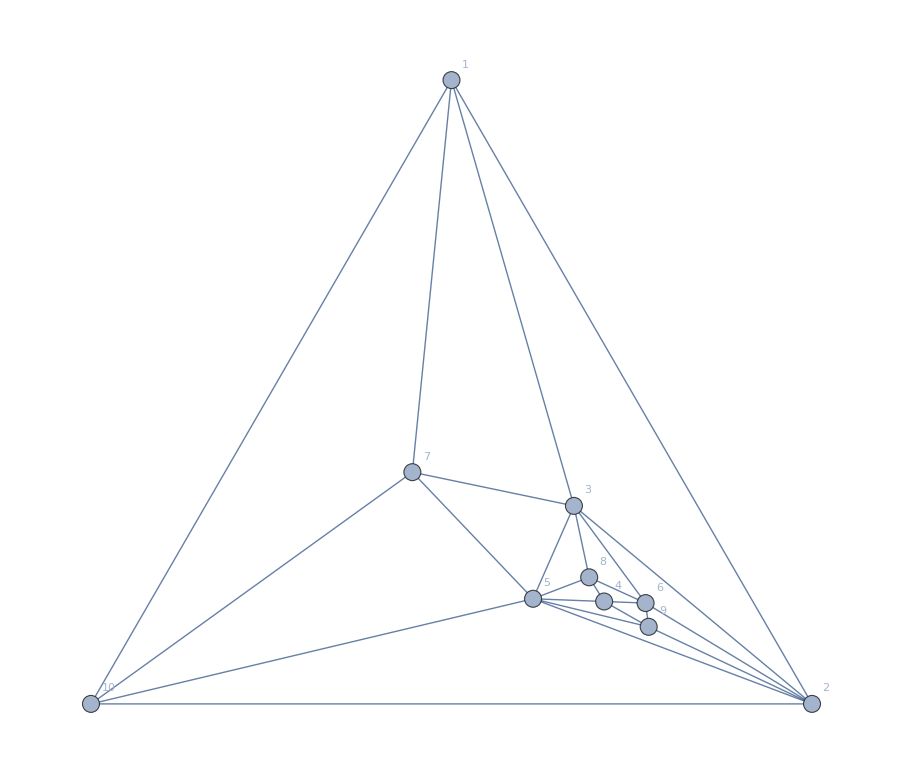

```mathematica
Graph[ReadGrof[111], VertexLabels->"Name",GraphLayout->"TutteEmbedding"]
```

```mathematica
Monitor[
Table[
With[
{g=Graph[plantri[[i]]]},
Table[
With[
{f=FindFace[g,e]},
{i,e,CalcQuadri[g,f]}
]
,{e,EdgeList[g]}]
],
{i,1,2}
],{i,e}]
```

{{{1,1<->2,{18,14,8,6,2,0,{5,5,5,5}}},{1,1<->3,{18,14,8,6,2,0,{5,5,5,5}}},{1,1<->4,{18,14,8,6,2,0,{5,5,5,5}}},{1,1<->5,{18,14,8,6,2,0,{5,5,5,5}}},{1,1<->6,{18,14,8,6,2,0,{5,5,5,5}}},{1,2<->6,{18,14,8,6,2,0,{5,5,5,5}}},{1,2<->7,{18,14,8,6,2,0,{5,5,5,5}}},{1,2<->8,{18,14,8,6,2,0,{5,5,5,5}}},{1,2<->3,{18,14,8,6,2,0,{5,5,5,5}}},{1,3<->8,{18,14,8,6,2,0,{5,5,5,5}}},{1,3<->9,{18,14,8,6,2,0,{5,5,5,5}}},{1,3<->4,{18,14,8,6,2,0,{5,5,5,5}}},{1,4<->9,{18,14,8,6,2,0,{5,5,5,5}}},{1,4<->10,{18,14,8,6,2,0,{5,5,5,5}}},{1,4<->5,{18,14,8,6,2,0,{5,5,5,5}}},{1,5<->10,{18,14,8,6,2,0,{5,5,5,5}}},{1,5<->11,{18,14,8,6,2,0,{5,5,5,5}}},{1,5<->6,{18,14,8,6,2,0,{5,5,5,5}}},{1,6<->11,{18,14,8,6,2,0,{5,5,5,5}}},{1,6<->7,{18,14,8,6,2,0,{5,5,5,5}}},{1,7<->11,{18,14,8,6,2,0,{5,5,5,5}}},{1,7<->12,{18,14,8,6,2,0,{5,5,5,5}}},{1,7<->8,{18,14,8,6,2,0,{5,5,5,5}}},{1,8<->12,{18,14,8,6,2,0,{5,5,5,5}}},{1,8<->9,{18,14,8,6,2,0,{5,5,5,5}}},{1,9<->12,{18,14,8,6,2,0,{5,5,5,5}}},{1,9<->10,{18,14,8,6,2,0,{5,5,5,5}}},{1,10<->12,{18,14,8,6,2,0,{5,5,5,5}}},{1,10<->11,{18,14,8,6,2,0,{5,5,5,5}}},{1,11<->12,{18,14,8,6,2,0,{5,5,5,5}}}},{{2,1<->2,{34,32,14,18,6,0,{6,5,5,5}}},{2,1<->3,{34,32,14,18,6,0,{6,5,5,5}}},{2,1<->4,{34,32,14,18,6,0,{6,5,5,5}}},{2,1<->5,{34,32,14,18,6,0,{6,5,5,5}}},{2,1<->6,{34,32,14,18,6,0,{6,5,5,5}}},{2,1<->7,{34,32,14,18,6,0,{6,5,5,5}}},{2,2<->7,{34,27,14,13,4,0,{5,6,5,5}}},{2,2<->8,{39,27,19,8,3,0,{5,5,5,5}}},{2,2<->9,{39,27,19,8,3,0,{5,5,5,5}}},{2,2<->3,{34,27,14,13,4,0,{5,6,5,5}}},{2,3<->9,{39,27,19,8,3,0,{5,5,5,5}}},{2,3<->10,{39,27,19,8,3,0,{5,5,5,5}}},{2,3<->4,{34,27,14,13,4,0,{5,6,5,5}}},{2,4<->10,{39,27,19,8,3,0,{5,5,5,5}}},{2,4<->11,{39,27,19,8,3,0,{5,5,5,5}}},{2,4<->5,{34,27,14,13,4,0,{5,6,5,5}}},{2,5<->11,{39,27,19,8,3,0,{5,5,5,5}}},{2,5<->12,{39,27,19,8,3,0,{5,5,5,5}}},{2,5<->6,{34,27,14,13,4,0,{5,6,5,5}}},{2,6<->12,{39,27,19,8,3,0,{5,5,5,5}}},{2,6<->13,{39,27,19,8,3,0,{5,5,5,5}}},{2,6<->7,{34,27,14,13,4,0,{5,6,5,5}}},{2,7<->13,{39,27,19,8,3,0,{5,5,5,5}}},{2,7<->8,{39,27,19,8,3,0,{5,5,5,5}}},{2,8<->13,{34,27,14,13,4,0,{5,5,5,6}}},{2,8<->14,{34,32,14,18,6,0,{5,5,6,5}}},{2,8<->9,{34,27,14,13,4,0,{5,5,5,6}}},{2,9<->14,{34,32,14,18,6,0,{5,5,6,5}}},{2,9<->10,{34,27,14,13,4,0,{5,5,5,6}}},{2,10<->14,{34,32,14,18,6,0,{5,5,6,5}}},{2,10<->11,{34,27,14,13,4,0,{5,5,5,6}}},{2,11<->14,{34,32,14,18,6,0,{5,5,6,5}}},{2,11<->12,{34,27,14,13,4,0,{5,5,5,6}}},{2,12<->14,{34,32,14,18,6,0,{5,5,6,5}}},{2,12<->13,{34,27,14,13,4,0,{5,5,5,6}}},{2,13<->14,{34,32,14,18,6,0,{5,5,6,5}}}}}

```mathematica
Reduce[(2*(alfa+beta)-lambda)==5*alfa1&&alfa+beta==g,g]
```

alfa==(5 alfa1)/2-beta+lambda/2&&g==(5 alfa1)/2+lambda/2